```mathematica
Clear["Global`*"]
```

# Population growth

Consider the population of a biological species, denoted by p. As a first approach it seems reasonable that the number of children increases with the population. The number of children stands for the reproduction rate of the species, denoted as dc/dt, the temporal change of the population at each time instant. For the sake of simplicity one may consider that the reproduction rate is proportional to p.
...

## Analytic solution

State the math model (eqn, initial condition, assumptions on constants and parameters):

```mathematica
mdl={eqn=p'[t]==k p[t],inc=p[0]==p0};
$Assumptions=k>0&&p[0]>0;
```

Solve the model for p at some values of t:

```mathematica
sln=DSolve[mdl,p[t],t]
```

{{p[t]→ⅇ^(k t) p0}}

Assign the solution to p(t):

```mathematica
p[t_]=p[t]/.sln[[1]];
```

Verify that p(t) satisfies the diff eqn and the init condition:

```mathematica
eqn//FullSimplify
```

True

```mathematica
inc//FullSimplify
```

True

Find values at extreme points:

```mathematica
p[0]
```

p0

```mathematica
Limit[p[t],t->Infinity]
```

∞

Assume values for p0 and k:

```mathematica
p0=1;k=1;
```

Plot the solution:

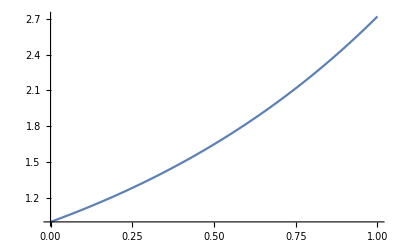

```mathematica
Plot[p[t],{t,0,1}]
```

```mathematica
Clear["Global`*"]
```

## Numerical solution

State the model:

```mathematica
mdl={eqn=p'[t]==k p[t],inc=p[0]==p0};
```

Assign values:

```mathematica
p0=1;k=1;
```

Solve:

```mathematica
nsln =NDSolve[mdl,p,{t,0,1}]
```

{{p→InterpolatingFunction[{{0., 1.}}, <>]}}

Find some typical values at known or extreme values, like boundary conditions, zero, infinity and so on:

```mathematica
p[0]/.nsln
```

{1.}

```mathematica
p[1]/.nsln
```

{2.71828}

```mathematica
p[Infinity]/.nsln
```

{InterpolatingFunction[{{0., 1.}}, <>][∞]}

```mathematica
Limit[(p[x]/.nsln),x->Infinity]
```

{Limit[InterpolatingFunction[{{0., 1.}}, <>][x],x→∞]}

Plot the numeric solution:

```mathematica
Plot[Evaluate[p[t]/.nsln],{t,0,1}]
```

-Graphics-

Compare the solution with the model differential equation (not working yet :(

```mathematica
Plot[Evaluate[eqn/.nsln],{t,0,1},PlotRange->{-0.00015,0.00015}]
```

-Graphics-